```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"..","Data"}]];
(*Functions for SCS-CNx case*)
Clear[CC,Pχ,JIavg,JSavg,JSavg2,CC1,CDFχ,χ2avg,χavg,CC0,CC01,Pχ0,χavg0,χ2avg0,CDFχ0,ϑ]
CC[DI_?NumericQ,γs_?NumericQ,β_?NumericQ,ρb_?NumericQ,ϑ_?NumericQ]:=CC[DI,γs,β,ρb,ϑ]=1/NIntegrate[((1- β ϑ x)^(((1-β) γs)/(β (1-β ϑ)))(1-x)^((γs (1-ϑ))/(1-β ϑ)))/x^(1-γs/(DI(1+ρb))),{x,0,1},AccuracyGoal->6](*w^((γs (1-ϑ))/(1-β ϑ)+((1-β) γs)/(β (1-β ϑ)))*)
CC1[DI_,γs_,β_,ρb_,ϑ_]:=Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/(DI(1+ρb))]/(Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/(DI(1+ρb))])1/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/(DI (1+ρb)) ,(γs(1-ϑ))/(1-β ϑ)+1+γs/(DI(1+ρb)),β ϑ]
Pχ[x_,DI_,γs_,β_,ρb_,ϑ_]:=CC1[DI,γs,β,ρb,ϑ]((1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))(1-x)^((γs (1-ϑ))/(1-β ϑ)))/x^(1-γs/(DI(1+ρb)))(*ⅇ^(-γs ϑ x) (1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))*)
CDFχ[x_,DI_,γs_,β_,ρb_,ϑ_]:=CC1[DI,γs,β,ρb,ϑ](DI x^(γs/(DI+DI ρb)) (1+ρb) AppellF1[γs/(DI+DI ρb),-(γs (-1+ϑ))/(-1+β ϑ),-((-1+β) γs)/(β (-1+β ϑ)),1+γs/(DI+DI ρb),x,x β ϑ])/γs
(*Transition PDF average fluxes*)
JIavg[DI_?NumericQ,γs_?NumericQ,β_?NumericQ,w_?NumericQ,ρb_?NumericQ,ϑ_?NumericQ]:=JIavg[DI,γs,β,w,ρb,ϑ]=NIntegrate[x(1-u)^2/(1-x)^2 γs/(1-β u) ⅇ^(-γs/(1-β  u) (1-u)/(1-x) (x-u))Pχ[u,DI,γs,β,ρb,ϑ]UnitStep[x-u],{u,0,1},{x,0,1},AccuracyGoal->3](*Accuracy Goal was 3*)
JSavg[DI_?NumericQ,γs_?NumericQ,β_?NumericQ,w_?NumericQ,ρb_?NumericQ,ϑ_?NumericQ]:=JSavg[DI,γs,β,w,ρb,ϑ]=NIntegrate[x 1/(1-(-x^2 β ϑ+(x-x(1-β) ϑ))/(1-x ϑ))γs ⅇ^(-γs(1/(β (-1+β ϑ)) ( Log[((1-x)/(1-u))^(β (1-ϑ))((1-x β ϑ)/(1-u β ϑ))^(1-β)])))Pχ[u,DI,γs,β,ρb,ϑ]UnitStep[x-u],{u,0,1},{x,0,1},AccuracyGoal->3](*-γs Log[((1-x)/(1-u))^(-(β (1-ϑ))/(β (1-β ϑ)))((1-x β ϑ)/(1-u β ϑ))^(-(1-β)/(β (1-β ϑ)))]*)
(*2nd equivalent version that is not used*)
JSavg2[DI_?NumericQ,γs_?NumericQ,β_?NumericQ,w_?NumericQ,ρb_?NumericQ,ϑ_?NumericQ]:=JSavg2[DI,γs,β,w,ρb,ϑ]=NIntegrate[x 1/(1-(-x^2 β ϑ+(x-x(1-β) ϑ))/(1-x ϑ))γs ⅇ^(-γs(w/(β (-1+β ϑ)) ( Log[(w-x)^(β (1-ϑ))(w-x β ϑ)^(1-β)])))CC[DI,γs,β,ρb,ϑ]/u^(1-(γs w)/(DI(1+ρb)))UnitStep[x-u],{u,0,1},{x,0,1},AccuracyGoal->3]
(*Function for Consistency with Ito Jumps*)
ϑold[DI_,γs_,β_,ρb_,ξ_]:=Max[-(DI(1+ρb)(2(1+β^2)-ξ))/γs+ⅇ^(-((ξ-β) DI(1+ρb))/γs(1+β)),0]
Clear[ϑ,ξ1,ξ2,ξ3,ξ4]
ξ1=2; (*3.5 Lower Number Lowers Curve*)
ξ2=2; (*4.1 Higher Number Lowers Curve*)
ξ3=.55;(*1.35*)
ξ4=3.;
(*ϑ[DI_,γs_,β_,ρb_]:=Max[-(DI(1+ρb))/(γs^(2(1-ξ1 β^2)))(ξ3+ξ4(β-β^2))+ⅇ^(-2(1-ξ2 β^2)(DI(1+ρb))/(γs^(1-.5 β^2))),0]*)
ξ1n=2;
ξ2n=0.5;
ξ3n=2.75;
ξ4n=-16.29;
ξ5n=-0.2;
ξ6n=0.566;
ξ7n=-1.352;
ξ8n=5;
ξ9n=57.1;
ξ10n=2.66;
ϑ[DI_,γs_,β_,ρb_]:=Piecewise[{{Max[ⅇ^(-2(1-ξ1n β^2)(DI(1+ρb))/(γs^(1-.5 β^2)))-(ξ2n+ξ3n β+ξ4n β^4.5)(DI(1+ρb))/(γs^(2(1-ξ1n β^2))),0],0<=β<=.5},{Max[ⅇ^(-(DI(1+ρb))/γs^(7/8))-(ξ7n+ξ8n β+ξ9n β^13.5)((DI(1+ρb))/γs)^(1+ξ5n +ξ6n β^1.5),0],.5<β<1},{Max[-(DI(1+ρb))/γs ξ10n+ⅇ^(-(DI(1+ρb))/γs),0],β==1}}]

(*First adn Second Moments*)
χavg[DI_,γs_,β_,ρb_,ϑ_]:=γs/(γs+DI(1+ρb)(1+γs(1-ϑ)/(1-ϑ β)))Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),1+γs/(DI (1+ρb)) ,(γs(1-ϑ))/(1-β ϑ)+2+γs/(DI(1+ρb)),β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/(DI (1+ρb)) ,(γs(1-ϑ))/(1-β ϑ)+1+γs/(DI(1+ρb)),β ϑ]

χ2avg[DI_,γs_,β_,ρb_,ϑ_]:=(γs(DI(1+ρb)+γs))/((γs+DI(1+ρb)(1+γs(1-ϑ)/(1-ϑ β))) (γs+DI(1+ρb)(2+γs(1-ϑ)/(1-ϑ β))))Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),2+γs/(DI (1+ρb)) ,(γs(1-ϑ))/(1-β ϑ)+3+γs/(DI(1+ρb)),β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/(DI (1+ρb)) ,(γs(1-ϑ))/(1-β ϑ)+1+γs/(DI(1+ρb)),β ϑ]
(*Functions for the scs-cn case where β=0*)
CC0[DI_?NumericQ,γs_?NumericQ,β_?NumericQ,ρb_?NumericQ,ϑ_?NumericQ]:=CC[DI,γs,β,ρb,ϑ]=1/NIntegrate[(ⅇ^(-γs ϑ x)(1-x)^(γs (1-ϑ)))/x^(1-γs/(DI(1+ρb))),{x,0,1},AccuracyGoal->6]
CC01[DI_,γs_,β_,ρb_,ϑ_]:=Gamma[γs (1-ϑ)+1+γs/(DI(1+ρb))]/(Gamma[γs (1-ϑ)+1]Gamma[γs/(DI(1+ρb))]Hypergeometric1F1[γs/(DI(1+ρb)),1+γs (1-ϑ)+γs/(DI(1+ρb)),-γs ϑ ])
Pχ0[x_,DI_,γs_,β_,ρb_,ϑ_]:=CC01[DI,γs,β,ρb,ϑ](ⅇ^(-γs ϑ x)(1-x)^(γs (1-ϑ)))/x^(1-γs/(DI(1+ρb)))(*ⅇ^(-γs ϑ x) (1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))*)
CDFχ0[x_,DI_,γs_,β_,w_,ρb_,ϑ_]:=CC0[DI,γs,β,ρb,ϑ](DI x^(γs/(DI+DI ρb)) (1+ρb) Hypergeometric2F1[γs (-1+ϑ),γs/(DI+DI ρb),1+γs/(DI+DI ρb),x])/γs
(*Transition PDF average fluxes*)
JIavg0[DI_?NumericQ,γs_?NumericQ,β_?NumericQ,w_?NumericQ,ρb_?NumericQ,ϑ_?NumericQ]:=JIavg0[DI,γs,β,w,ρb,ϑ]=NIntegrate[x(1-u)^2/(1-x)^2 γs/(1-β u) ⅇ^(-γs/(1-β  u) (1-u)/(1-x) (x-u))Pχ0[u,DI,γs,β,ρb,ϑ]UnitStep[x-u],{u,0,1},{x,0,1},AccuracyGoal->3]
JSavg0[DI_?NumericQ,γs_?NumericQ,β_?NumericQ,w_?NumericQ,ρb_?NumericQ,ϑ_?NumericQ]:=JSavg0[DI,γs,β,w,ρb,ϑ]=NIntegrate[x 1/(1-(x-x ϑ)/(1-x ϑ))γs ⅇ^(-γs Log[ⅇ^((x-u) ϑ) ((1-x)/(1-u))^(-1+ϑ)])Pχ0[u,DI,γs,β,ρb,ϑ]UnitStep[x-u],{u,0,1},{x,0,1},AccuracyGoal->3](*-γs Log[((1-x)/(1-u))^(-(β (1-ϑ))/(β (1-β ϑ)))((1-x β ϑ)/(1-u β ϑ))^(-(1-β)/(β (1-β ϑ)))]*)
χavg0[DI_,γs_,β_,ρb_,ϑ_]:=γs/(γs+DI(1+ρb)(1+γs (1-ϑ)))Hypergeometric1F1[1+γs/(DI(1+ρb)),2+γs (1-ϑ)+γs/(DI(1+ρb)),-γs ϑ ]/Hypergeometric1F1[γs/(DI(1+ρb)),1+γs (1-ϑ)+γs/(DI(1+ρb)),-γs ϑ ]
χ2avg0[DI_,γs_,β_,ρb_,ϑ_]:=(γs(DI(1+ρb)+γs))/((γs+DI(1+ρb)(1+γs(1-ϑ))) (γs+DI(1+ρb)(2+γs(1-ϑ))))Hypergeometric1F1[2+γs/(DI(1+ρb)),3+γs (1-ϑ)+γs/(DI(1+ρb)),-γs ϑ ]/Hypergeometric1F1[γs/(DI(1+ρb)),1+γs (1-ϑ)+γs/(DI(1+ρb)),-γs ϑ ]
```

```mathematica
(*Limit for transition PDF term of the SCS-CN case where β=0*)
Limit[γs Log[((1-x)/(1-u))^(-(1-ϑ)/(1-β ϑ))((1-x β ϑ)/(1-u β ϑ))^(-(1-β)/(β (1-β ϑ)))],β->0]
Limit[(-x^2 β ϑ+(x-x(1-β) ϑ))/(1-x ϑ),β->0]
(-x^2 β ϑ+(x-x(1-β) ϑ))/(1-x ϑ)/.β->0
```

γs Log[ⅇ^((-u+x) ϑ) ((-1+x)/(-1+u))^(-1+ϑ)]

(x (-1+ϑ))/(-1+x ϑ)

(x-x ϑ)/(1-x ϑ)

```mathematica
(*Simplify the Function for the Average where a=γs/(DI(1+ρb)) and b=γs (1-ϑ)*)
(Gamma[b+1+a]Gamma[1+a])/(Gamma[b+2+a]Gamma[a])//FullSimplify
(Gamma[b+1+a]Gamma[2+a])/(Gamma[b+3+a]Gamma[a])//FullSimplify
```

a/(1+a+b)

(a (1+a))/((1+a+b) (2+a+b))

```mathematica
(*Checks*)
(**)
Clear[w,β,γ,ρb,DI];
w=10;
β=.05;
γ=w/2;
ρb=0;
λ=.2;
ξ=1.75;
DI=1.5;(*DI=(γ k)/λ*)
CC[DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
CC1[DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
 CDFχ[.5,DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
NIntegrate[Pχ[x,DI,γ,β,ρb,ϑ[DI,γ,β,ρb]],{x,0,.5}]
NIntegrate[x Pχ[x,DI,γ,β,ρb,ϑ[DI,γ,β,ρb]],{x,0,1}]
χavg[DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
NIntegrate[x^2 Pχ[x,DI,γ,β,ρb,ϑ[DI,γ,β,ρb]],{x,0,1}]
χ2avg[DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
(**)
```

176.925

176.925

0.702949

0.702949

0.409049

0.409049

0.196862

0.196862

```mathematica
χ2avg0[DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
```

0.255493

```mathematica
Clear[w,β,γ,ρb,DI,ξ];
w=20;
β=0;
γ=w/2;
ρb=0;
λ=.2;
ξ=1.77;
DI=1.5;(*DI=(γ k)/λ*)
CC0[DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
1/CC01[DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
CDFχ0[.5,DI,γ,β,w,ρb,ϑ[DI,γ,β,ρb]]
NIntegrate[Pχ0[x,DI,γ,β,ρb,ϑ[DI,γ,β,ρb]],{x,0,.5}]
NIntegrate[x Pχ0[x,DI,γ,β,ρb,ϑ[DI,γ,β,ρb]],{x,0,1}]
χavg0[DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
NIntegrate[x^2 Pχ0[x,DI,γ,β,ρb,ϑ[DI,γ,β,ρb]],{x,0,1}]
χ2avg0[DI,γ,β,ρb,ϑ[DI,γ,β,ρb]]
```

31310.8

0.0000319378

10.3319

0.556131

0.483497

0.483497

0.255703

0.255703

```mathematica
(*Simulation Check*)
(**)
Clear[yr,w,β,γ,ρb,DI,sol,Ft];
yr=200;(*Number of years*)
(**)
w=50;(*10*)
β=.1;(*.45*)
γ=w/2;
ρb=0.;
λ=.15;
DI=1.05;(*1.5 DI=(γ k)/λ*)
ξ=1.77;
(**)
Ft[x_,z_,w_,β_]:=(z w (1-β x))/(w(1-x)+z w (1-β x))(*Fraction of Threshold Saturated area for the SCS-CN method*)
sol=NDSolve[{ss'[t]==-(DI/γ λ(1+ρb)) ss[t],ss[0]==.2,tnext[0]==RandomReal[ExponentialDistribution[λ]],WhenEvent[t==tnext[t],{RR1=RandomReal[ExponentialDistribution[γ]],ss[t]->ss[t]+RR1(1-(Ft[ss[t],RR1,w,β]+(1-Ft[ss[t],RR1,w,β])β ss[t])),tnext[t]->tnext[t]+RandomReal[ExponentialDistribution[λ]]}]},{ss,tnext},{t,0,365 yr},DiscreteVariables->{tnext}]
```

{{ss→InterpolatingFunction[{{0., 73000.}}, <>],tnext→InterpolatingFunction[…]}}

```mathematica
ϑ[1,2,.1,0]
```

0.163273

```mathematica
Clear[ϑ1];
ξ=1.77;
ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β,w,ρb,ϑ1]==JSavg[DI,γ,β,w,ρb,ϑ1],{ϑ1,ϑ[DI,γ,β,ρb]*.75,.1,.999},AccuracyGoal->7]
ϑ[DI,γ,β,ρb]
JIavg[DI,γ,β,w,ρb,ϑ1]-JSavg[DI,γ,β,w,ρb,ϑ1]
JIavg[DI,γ,β,w,ρb,ϑ[DI,γ,β,ρb]]-JSavg[DI,γ,β,w,ρb,ϑ[DI,γ,β,ρb]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.922895

0.918181

-0.0000391565

0.00041358

```mathematica
JIavg[DI,γ,β,w,ρb,.55]
```

0.

```mathematica
ϑ[DI,γ,β,ρb]
```

0.960431

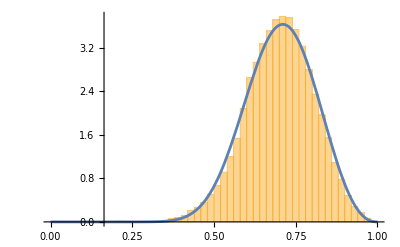

```mathematica
(*Compare simulation and analytical result*)
pt3=Plot[{Pχ[x,DI,γ,β,ρb,ϑ[DI,γ,β,ρb]](*JSavgx[x,DI,γ,β,w,ρb,ϑ[DI,γ,β,ρb]]*)},{x,0,1},PlotRange->All];
soilsim1=Flatten[Table[ss[t]/.sol,{t,0,365 yr,.1}]];
pt1=Histogram[{soilsim1},50,"PDF"];
Show[pt1,pt3,PlotRange->All]
```

```mathematica
(*Compare simulation and analytical result*)
pt3=Plot[{Pχ[x,DI,γ,β,ρb,ϑ[DI,γ,β,ρb]],JSavgx[x,DI,γ,β,w,ρb,ϑ1]},{x,0,1},PlotRange->All];
soilsim1=Flatten[Table[ss[t]/.sol,{t,0,365 yr,.1}]];
pt1=Histogram[{soilsim1},50,"PDF"];
Show[pt1,pt3,PlotRange->All]
```

-Graphics-

```mathematica
JIavgx[x_?NumericQ,DI_?NumericQ,γs_?NumericQ,β_?NumericQ,w_?NumericQ,ρb_?NumericQ,ϑ_?NumericQ]:=JIavgx[x,DI,γs,β,w,ρb,ϑ]=NIntegrate[(1-u)^2/(1-x)^2 γs/(1-β u) ⅇ^(-γs/(1-β  u) (1-u)/(1-x) (x-u))Pχ[u,DI,γs,β,ρb,ϑ]UnitStep[x-u],{u,0,1},AccuracyGoal->3](*Accuracy Goal was 3*)
JSavgx[x_?NumericQ,DI_?NumericQ,γs_?NumericQ,β_?NumericQ,w_?NumericQ,ρb_?NumericQ,ϑ_?NumericQ]:=JSavgx[x,DI,γs,β,w,ρb,ϑ]=NIntegrate[1/(1-(-x^2 β ϑ+(x-x(1-β) ϑ))/(1-x ϑ))γs ⅇ^(-γs(1/(β (-1+β ϑ)) ( Log[((1-x)/(1-u))^(β (1-ϑ))((1-x β ϑ)/(1-u β ϑ))^(1-β)])))Pχ[u,DI,γs,β,ρb,ϑ]UnitStep[x-u],{u,0,1},AccuracyGoal->3]
```

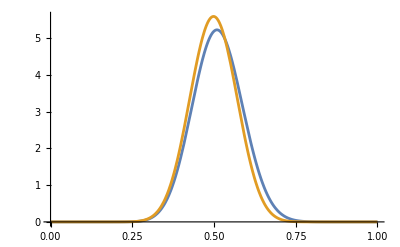

```mathematica
Plot[{JIavgx[x,DI,γ,β,w,ρb,ϑ1],JSavgx[x,DI,γ,β,w,ρb,ϑ1]},{x,0,1}]
```

```mathematica
With[{w=10,β=.1,γ=10/2,ρb=.4,DI=.5},ⅇ^(-1/(γ/(DI(1+ρb))) (1.75+0/(.1)))]
```

```mathematica
ξ=1.77;
β0=0;
Clear[TabC01,TabC02]
TabC01=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg0[DI,γ,β0,w,ρb,ϑ1]==JSavg0[DI,γ,β0,w,ρb,ϑ1],{ϑ1,Evaluate[Max[-(DI(2(1+β0^2)-ξ))/γ+ⅇ^(-((ξ-β0) DI(1+ρb))/γ(1+β0)),.005]],.005,.99},AccuracyGoal->3])},{γ,{10/(.25),10/(.5),10/1}},{DI,.35,3,.2}];
TabC02=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg0[DI,γ,β0,w,ρb,ϑ1]==JSavg0[DI,γ,β0,w,ρb,ϑ1],{ϑ1,Evaluate[Max[-(DI(2(1+β0^2)-ξ))/γ+ⅇ^(-((ξ-β0) DI(1+ρb))/γ(1+β0)),.005]],.005,.99},AccuracyGoal->3])},{γ,{10/1.5,10/2,10/2.5,10/5}},{DI,.35,3,.2}];
export0=Flatten[{TabC01,TabC02},1];
Export["ConsistencyConditionSimulation0.csv",export0]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.005} is at the edge of the search region {0.005,0.99} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

ConsistencyConditionSimulation0.csv

```mathematica
ξ=1.77;
β=.05;
Clear[TabC1,TabC2]
TabC1=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β,w,ρb,ϑ1]==JSavg[DI,γ,β,w,ρb,ϑ1],{ϑ1,Evaluate[Max[-(DI(2(1+β^2)-ξ))/γ+ⅇ^(-((ξ-β) DI(1+ρb))/γ(1+β)),.005]],.005,.99},AccuracyGoal->3])},{γ,{10/(.25),10/(.5),10/1}},{DI,.35,3,.2}];
TabC2=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β,w,ρb,ϑ1]==JSavg[DI,γ,β,w,ρb,ϑ1],{ϑ1,Evaluate[Max[-(DI(2(1+β^2)-ξ))/γ+ⅇ^(-((ξ-β) DI(1+ρb))/γ(1+β)),.005]],.005,.99},AccuracyGoal->3])},{γ,{10/1.5,10/2,10/2.5,10/5}},{DI,.35,3,.2}];
export=Flatten[{TabC1,TabC2},1];
Export["ConsistencyConditionSimulation.csv",export]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.63723 and 0.0012256 for the integral and error estimates.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::reged: The point {0.005} is at the edge of the search region {0.005,0.99} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

ConsistencyConditionSimulation.csv

```mathematica
ξ=1.77;
β1=.15
Clear[TabC11,TabC12]
TabC11=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β1,w,ρb,ϑ1]==JSavg[DI,γ,β1,w,ρb,ϑ1],{ϑ1,Evaluate[Max[-(DI(2(1+β1^2)-ξ))/γ+ⅇ^(-((ξ-β1) DI(1+ρb))/γ(1+β1)),.0055]],.005,.99},AccuracyGoal->3])},{γ,{10/(.25),10/(.5),10/1}},{DI,.35,3,.2}];
TabC12=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β1,w,ρb,ϑ1]==JSavg[DI,γ,β1,w,ρb,ϑ1],{ϑ1,Evaluate[Max[-(DI(2(1+β1^2)-ξ))/γ+ⅇ^(-((ξ-β1) DI(1+ρb))/γ(1+β1)),.0055]],.005,.99},AccuracyGoal->3])},{γ,{10/1.5,10/2,10/2.5,10/5}},{DI,.35,3,.2}];
export1=Flatten[{TabC11,TabC12},1];
Export["ConsistencyConditionSimulation1.csv",export1]
```

0.15

FindRoot::reged: The point {0.005} is at the edge of the search region {0.005,0.99} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.005} is at the edge of the search region {0.005,0.99} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.005} is at the edge of the search region {0.005,0.99} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

ConsistencyConditionSimulation1.csv

```mathematica
β2=.25
TabC21= Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β2,w,ρb,ϑ1]==JSavg[DI,γ,β2,w,ρb,ϑ1],{ϑ1,Evaluate[.95Max[-(DI(2-ξ)(1-β2))/γ+ⅇ^(-((ξ DI(1+ρb))/γ)(1+β2)),.0055]],.005,.99},AccuracyGoal->3])},{γ,{10/(.251),10/(.5),10/1}},{DI,.35,3,.2}];
TabC22=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β2,w,ρb,ϑ1]==JSavg[DI,γ,β2,w,ρb,ϑ1],{ϑ1,Evaluate[Max[-(DI(2-ξ)(1-β2))/γ+ⅇ^(-((ξ DI(1+ρb))/γ)(1+β2)),.0055]],.005,.99},AccuracyGoal->3])},{γ,{10/1.5,10/2.,10/2.5}},{DI,.35,3,.2}];
export2=Flatten[{TabC21,TabC22},1];
Export["ConsistencyConditionSimulation2.csv",export2]
```

0.25

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.87335 and 0.00258828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region {{0.75,0.875},{1.,0.99999999999999999999999999999997515343915057095724101573241897475}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand (3176.08 (1-u)^0.0987132 (1-0.245344 u)^15.9013 u^10.4286 (((1-x)/(1+«1»))^0.00465591 («1»)^0.75)^21.2017 x UnitStep[-u+x])/(1-(0.263968 x-0.245344 x^2)/(1-0.981376 x)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.75,0.875},{0.99999999999999999999999999999997515343915057095724101573241897475,0.99999999999999999999052776490999723314886968896283843924234350968}}.

NIntegrate::zeroregion: Integration region {{0.75,0.875},{1.,0.99999999999999999999999999999997515343915057095724101573241897475}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand (3176.08 (1-u)^0.0987132 (1-0.245344 u)^15.9013 u^10.4286 (((1-x)/(1+«1»))^0.00465591 («1»)^0.75)^21.2017 x UnitStep[-u+x])/(1-(0.263968 x-0.245344 x^2)/(1-0.981376 x)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.75,0.875},{0.99999999999999999999999999999997515343915057095724101573241897475,0.99999999999999999999052776490999723314886968896283843924234350968}}.

NIntegrate::zeroregion: Integration region {{0.75,0.875},{1.,0.99999999999999999999999999999997515343915057095724101573241897475}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::inumri: The integrand (3176.08 (1-u)^0.0987132 (1-0.245344 u)^15.9013 u^10.4286 ((«1»)^0.00465591 ((«1»)/(«1»))^0.75)^21.2017 x UnitStep[-1. u+x])/(1.-(1. (0.263968 x-0.245344 x^2))/(1.-0.981376 x)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.75,0.875},{0.99999999999999999999999999999997515343915057095724101573241897475,0.99999999999999999999052776490999723314886968896283843924234350968}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.928017-NIntegrate[(x 4. ⅇ^(«2» «2») Pχ[u,0.35,4.,0.25,0.,0.981376] UnitStep[x+Times[«2»]])/Plus[«2»],{u,0,1},{x,0,1},AccuracyGoal→3]} is not a list of numbers with dimensions {1} at {ϑ1} = {0.981376}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ConsistencyConditionSimulation2.csv

```mathematica
β3=.3
Clear[TabC31,TabC32]
TabC31=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β3,w,ρb,ϑ1]==JSavg[DI,γ,β3,w,ρb,ϑ1],{ϑ1,Max[-(DI(2(1+β3^2)-ξ))/γ+ⅇ^(-((ξ-β3) DI(1+ρb))/γ(1+β3)),.005],.005,.99},AccuracyGoal->3])},{γ,{10/(.25),10/(.5),10/1}},{DI,.35,3,.2}];
TabC32=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β3,w,ρb,ϑ1]==JSavg[DI,γ,β3,w,ρb,ϑ1],{ϑ1,Max[-(DI(2(1+β3^2)-ξ))/γ+ⅇ^(-((ξ-β3) DI(1+ρb))/γ(1+β3)),.005],.005,.99},AccuracyGoal->3])},{γ,{10/1.5,10/2,10/2.5,10/5}},{DI,.35,3,.2}];
export3=Flatten[{TabC31,TabC32},1];
Export["ConsistencyConditionSimulation3.csv",export3]
```

0.3

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.005} is at the edge of the search region {0.005,0.99} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.005} is at the edge of the search region {0.005,0.99} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

ConsistencyConditionSimulation3.csv

```mathematica
β4=.45
Clear[TabC41,TabC42]
TabC41=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β4,w,ρb,ϑ1]==JSavg[DI,γ,β4,w,ρb,ϑ1],{ϑ1,Max[-(DI(2(1+β4^2)-ξ))/γ+ⅇ^(-((ξ-β4) DI(1+ρb))/γ(1+β4)),.005],.005,.99},AccuracyGoal->3])},{γ,{10/(.25),10/(.5),10/1}},{DI,.35,3,.2}];
TabC42=Table[{DI,(ϑ1=ϑ1/.FindRoot[JIavg[DI,γ,β4,w,ρb,ϑ1]==JSavg[DI,γ,β4,w,ρb,ϑ1],{ϑ1,Max[-(DI(2(1+β4^2)-ξ))/γ+ⅇ^(-((ξ-β4) DI(1+ρb))/γ(1+β4)),.005],.005,.99},AccuracyGoal->3])},{γ,{10/1.5,10/2,10/2.5,10/5}},{DI,.35,3,.2}];
export4=Flatten[{TabC41,TabC42},1];
Export["ConsistencyConditionSimulation4.csv",export4]
```

0.45

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindRoot::reged: The point {0.005} is at the edge of the search region {0.005,0.99} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ConsistencyConditionSimulation4.csv

```mathematica
(*Plot β Dependency of Functions *)
```

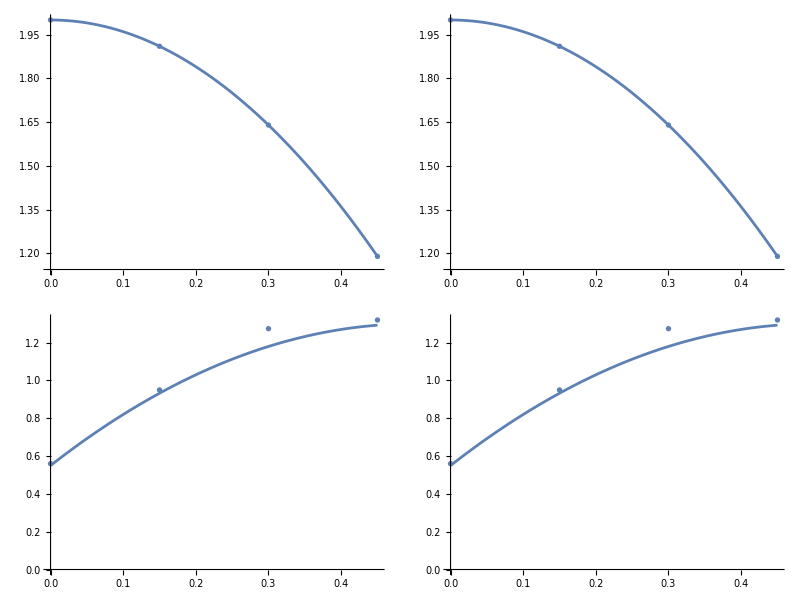

```mathematica
pa11=Plot[2-4 β^2,{β,0,.45}];
pa12=ListPlot[{{β0,2},{β1,1.91},{β3,1.64},{β4,1.19}}];
pa21=Plot[2-4 β^2,{β,0,.45}];
pa22=ListPlot[{{β0,2},{β1,1.91},{β3,1.64},{β4,1.19}}];
pa31=Plot[{1.3-3(β-.5)^2},{β,0,.45}];
pa32=ListPlot[{{β0,.56},{β1,.95},{β3,1.274},{β4,1.32}}];
Grid[{{Show[pa12,pa11,ImageSize->300],Show[pa22,pa21,ImageSize->300]},{Show[pa32,pa31,ImageSize->300],Show[pa32,pa31,ImageSize->300]}}]
```

{40.,20.,10,6.66667,5,4.}

{40.,20.,10,6.66667,5,4.,2}

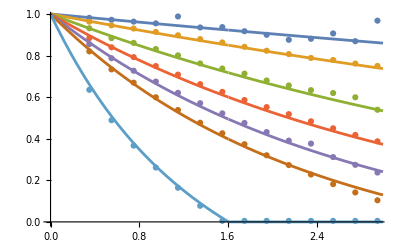

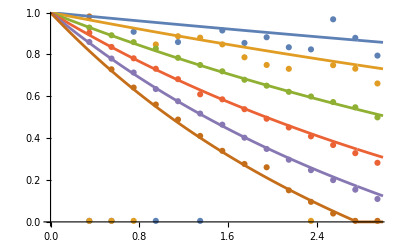

14

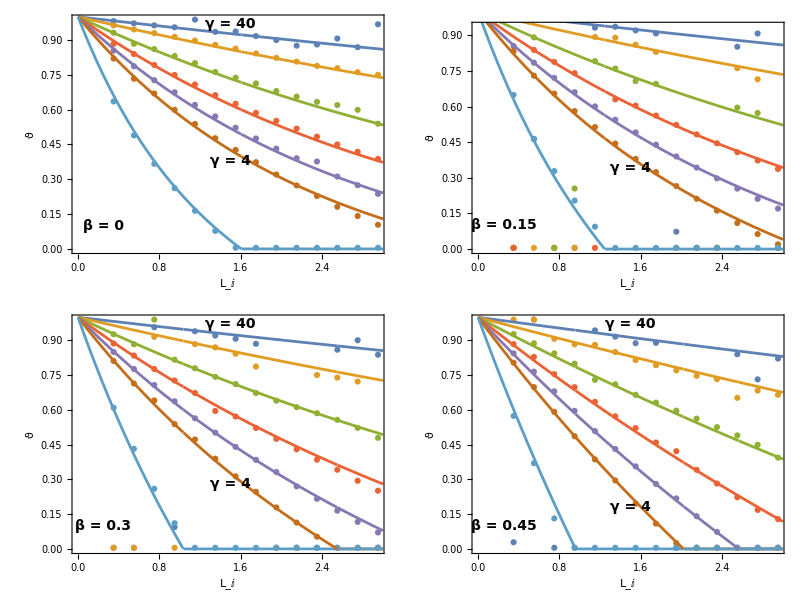

```mathematica
Clear[w]
ρb=0;
w=10;
γlist={w/(.25),w/(.5),w/1,w/1.5,w/2,w/2.5}
γ2list={w/(.25),w/(.5),w/1,w/1.5,w/2,w/2.5,w/5}

import0=Import["ConsistencyConditionSimulation0.csv"];
import=Import["ConsistencyConditionSimulation.csv"];
import1=Import["ConsistencyConditionSimulation1.csv"];
import2=Import["ConsistencyConditionSimulation2.csv"];
import3=Import["ConsistencyConditionSimulation3.csv"];
import4=Import["ConsistencyConditionSimulation4.csv"];
(**)
β0=0.0;
β=.05;
β1=.15;
β2=.25;
β3=.3;
β4=.45;
AnalData0=Plot[{Evaluate[Table[ϑ[DI,γ2list[[i]],β0,ρb],{i,1,Length[γ2list]}]]},{DI,0,3}];
AnalData=Plot[{Evaluate[Table[ϑ[DI,γ2list[[i]],β,ρb],{i,1,Length[γ2list]}]]},{DI,0,3}];
AnalData1=Plot[{Evaluate[Table[ϑ[DI,γ2list[[i]],β1,ρb],{i,1,Length[γ2list]}]]},{DI,0,3}];
AnalData2=Plot[{Evaluate[Table[ϑ[DI,γlist[[i]],β2,ρb],{i,1,Length[γlist]}]]},{DI,0,3}];

AnalData3=Plot[{Evaluate[Table[ϑ[DI,γ2list[[i]],β3,ρb],{i,1,Length[γ2list]}]]},{DI,0,3}];
AnalData4=Plot[{Evaluate[Table[ϑ[DI,γ2list[[i]],β4,ρb],{i,1,Length[γ2list]}]]},{DI,0,3}];
(**)
Show[ListPlot[ToExpression@import0],AnalData0,ImageSize->400]
Show[ListPlot[ToExpression@import2],AnalData2,ImageSize->400]
(**)
FontSize1=14
Texta=Graphics[{Text[Style["β = 0",FontSize1,Bold,Background->None],{.25,.1},{0,0},{1,0}],Text[Style["γ = 4",FontSize1,Bold,Background->None],{1.5,.38},{0,0},{1,-.5}],Text[Style["γ = 40",FontSize1,Bold,Background->None],{1.5,.97},{0,0},{1,-.07}]}];
Textb=Graphics[{Text[Style["β = 0.15",FontSize1,Bold,Background->None],{.25,.1},{0,0},{1,0}],Text[Style["γ = 4",FontSize1,Bold,Background->None],{1.5,.34},{0,0},{1,-.55}],Text[Style["γ = 40",FontSize1,Bold,Background->None],{1.5,.97},{0,0},{1,-.07}]}];
Textc=Graphics[{Text[Style["β = 0.3",FontSize1,Bold,Background->None],{.25,.1},{0,0},{1,0}],Text[Style["γ = 4",FontSize1,Bold,Background->None],{1.5,.28},{0,0},{1,-.6}],Text[Style["γ = 40",FontSize1,Bold,Background->None],{1.5,.97},{0,0},{1,-.07}]}];
Textd=Graphics[{Text[Style["β = 0.45",FontSize1,Bold,Background->None],{.25,.1},{0,0},{1,0}],Text[Style["γ = 4",FontSize1,Bold,Background->None],{1.5,.18},{0,0},{1,-.8}],Text[Style["γ = 40",FontSize1,Bold,Background->None],{1.5,.97},{0,0},{1,-.07}]}];
(**)
Labela=Graphics[{Text[Style["a)",16,Bold,Background->White],{-.35,1},{0,0},{1,0}]}];
Labelb=Graphics[{Text[Style["b)",16,Bold,Background->White],{-.35,1},{0,0},{1,0}]}];
Labelc=Graphics[{Text[Style["c)",16,Bold,Background->White],{-.35,1},{0,0},{1,0}]}];
Labeld=Graphics[{Text[Style["d)",16,Bold,Background->White],{-.35,1},{0,0},{1,0}]}];

(**)


figC1Export=Grid[{{Show[ListPlot[ToExpression@import0,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{Style[ϑ,FontSize->18],""},{Style[Subscript[L, I],FontSize->16],""}},LabelStyle->Directive[12,Bold]],AnalData0,Texta,Labela,ImageSize->400,PlotRangeClipping->False],Show[ListPlot[ToExpression@import1,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{Style[ϑ,FontSize->18],""},{Style[Subscript[L, I],FontSize->16],""}},LabelStyle->Directive[12,Bold]],AnalData1,Textb,Labelb,ImageSize->400,PlotRangeClipping->False]},{Show[ListPlot[ToExpression@import3,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{Style[ϑ,FontSize->18],""},{Style[Subscript[L, I],FontSize->16],""}},LabelStyle->Directive[12,Bold]],AnalData3,Textc,Labelc,ImageSize->400,PlotRangeClipping->False],Show[ListPlot[ToExpression@import4,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{Style[ϑ,FontSize->18],""},{Style[Subscript[L, I],FontSize->16],""}},LabelStyle->Directive[12,Bold]],AnalData4,Textd,Labeld,ImageSize->400,PlotRangeClipping->False]}},Spacings->{-1,-.25}]
```

```mathematica
SetDirectory["C:/Users/Mark S. Bartlett/Dropbox/Research/ReverseJumps/LateX"];
Export["FigureC1.eps",figC1Export];
```

0.2

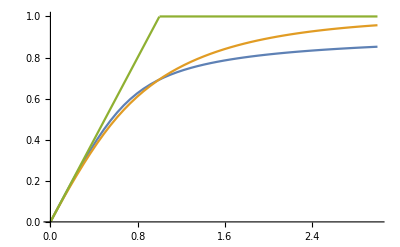

```mathematica
(*PLot Budyko Type Curve for SCS-CN method*)

β=.2
w=50;
γ=w/2;
Plot[{DI χavg[DI,γ,β,w,ρb,ϑ[DI,γ,β,ρb,ξ]],(DI(1-ⅇ^-DI)Tanh[1/DI])^0.5,DI UnitStep[1-DI]+1 UnitStep[DI-1]},{DI,.001,3}]
```

```mathematica
(*Simulation Check*)
(**)
Clear[yr,β,ρb,Ft,sol1,sol2,sol3,sol4];
Clear[w1,w2,w3,w4,DI1,DI2,DI3,DI4]
yr=150;(*Number of years*)
(**)
β=.7;(*.15*)
ρb=0.;
λ=.2;
(**)
w1=10;
γ1=w1/2.5;
w2=40;(*40*)
γ2=w2/2.5;
w3=10;
γ3=w3/2.5;
w4=40;(*40*)
γ4=w4/2.5;
(**)
DI1=1.5;(*DI=(γ k)/λ*)
DI2=1.5;(*DI=(γ k)/λ*)
DI3=0.5;(*DI=(γ k)/λ*)
DI4=0.5;(*DI=(γ k)/λ*)
(**)
Ft[x_,z_,w_,β_]:=(z w (1-β x))/(w(1-x)+z w (1-β x))(*Fraction of Threshold Saturated area for the SCS-CN method*)
sol1=NDSolve[{ss'[t]==-(DI1/γ1 λ(1+ρb)) ss[t],ss[0]==.2,tnext[0]==RandomReal[ExponentialDistribution[λ]],WhenEvent[t==tnext[t],{RR1=RandomReal[ExponentialDistribution[γ1]],ss[t]->ss[t]+RR1(1-(Ft[ss[t],RR1,w1,β]+(1-Ft[ss[t],RR1,w1,β])β ss[t])),tnext[t]->tnext[t]+RandomReal[ExponentialDistribution[λ]]}]},{ss,tnext},{t,0,365 yr},DiscreteVariables->{tnext}]
sol2=NDSolve[{ss'[t]==-(DI2/γ2 λ(1+ρb)) ss[t],ss[0]==.2,tnext[0]==RandomReal[ExponentialDistribution[λ]],WhenEvent[t==tnext[t],{RR1=RandomReal[ExponentialDistribution[γ2]],ss[t]->ss[t]+RR1(1-(Ft[ss[t],RR1,w2,β]+(1-Ft[ss[t],RR1,w2,β])β ss[t])),tnext[t]->tnext[t]+RandomReal[ExponentialDistribution[λ]]}]},{ss,tnext},{t,0,365 yr},DiscreteVariables->{tnext}]
sol3=NDSolve[{ss'[t]==-(DI3/γ3 λ(1+ρb)) ss[t],ss[0]==.2,tnext[0]==RandomReal[ExponentialDistribution[λ]],WhenEvent[t==tnext[t],{RR1=RandomReal[ExponentialDistribution[γ3]],ss[t]->ss[t]+RR1(1-(Ft[ss[t],RR1,w3,β]+(1-Ft[ss[t],RR1,w3,β])β ss[t])),tnext[t]->tnext[t]+RandomReal[ExponentialDistribution[λ]]}]},{ss,tnext},{t,0,365 yr},DiscreteVariables->{tnext}]
sol4=NDSolve[{ss'[t]==-(DI3/γ4 λ(1+ρb)) ss[t],ss[0]==.2,tnext[0]==RandomReal[ExponentialDistribution[λ]],WhenEvent[t==tnext[t],{RR1=RandomReal[ExponentialDistribution[γ4]],ss[t]->ss[t]+RR1(1-(Ft[ss[t],RR1,w4,β]+(1-Ft[ss[t],RR1,w4,β])β ss[t])),tnext[t]->tnext[t]+RandomReal[ExponentialDistribution[λ]]}]},{ss,tnext},{t,0,365 yr},DiscreteVariables->{tnext}]
```

{{ss→InterpolatingFunction[{{0., 54750.}}, <>],tnext→InterpolatingFunction[…]}}

{{ss→InterpolatingFunction[{{0., 54750.}}, <>],tnext→InterpolatingFunction[…]}}

{{ss→InterpolatingFunction[{{0., 54750.}}, <>],tnext→InterpolatingFunction[…]}}

«1 more identical outputs»

```mathematica
(*PLot THe Cruve Number*)
(*here w is considered in cm... hence the factor of 10*)
MinCN1=MinCN=25400./(10 w1(1-0)+254)
MinCN2=MinCN=25400./(10 w2(1-0)+254)
MinCN3=MinCN=25400./(10 w3(1-0)+254)
MinCN4=MinCN=25400./(10 w4(1-0)+254)

Cnplot1=Plot[{2540/(CN^2 w1) Pχ[(-2540+CN (25.4+ w1))/(CN w1),DI1,γ1,β,ρb,ϑ[DI1,γ1,β,ρb]]},{CN,MinCN1,100},PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_CN(CN)",""},{"CN",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[12,Bold]];
Cnplot2=Plot[{2540/(CN^2 w2) Pχ[(-2540+CN (25.4+ w2))/(CN w2),DI2,γ2,β,ρb,ϑ[DI2,γ2,β,ρb]]},{CN,MinCN2,100},PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_CN(CN)",""},{"CN",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[12,Bold]];
Cnplot3=Plot[{2540/(CN^2 w3) Pχ[(-2540+CN (25.4+ w3))/(CN w3),DI3,γ3,β,ρb,ϑ[DI3,γ3,β,ρb]]},{CN,MinCN3,100},PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_CN(CN)",""},{"CN",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[12,Bold]];
Cnplot4=Plot[{2540/(CN^2 w4) Pχ[(-2540+CN (25.4+ w4))/(CN w4),DI4,γ4,β,ρb,ϑ[DI4,γ4,β,ρb]*1]},{CN,MinCN4,100},PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_CN(CN)",""},{"CN",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[12,Bold]];
```

71.7514

38.8379

71.7514

38.8379

```mathematica
ϑ[DI4,γ4,β,ρb]
γ4
```

0.678882

16.

12

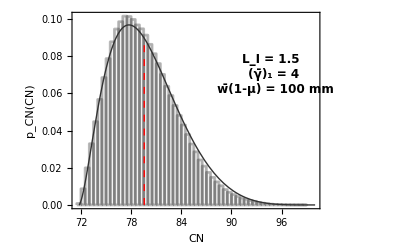

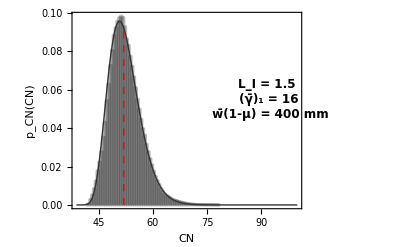

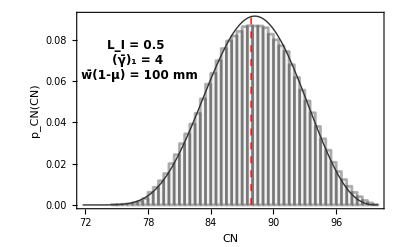

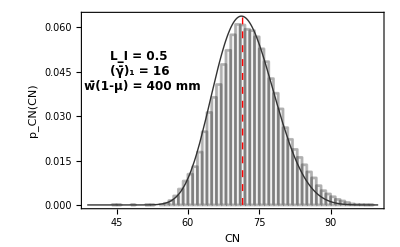

```mathematica
(*Compare simulation and analytical result*)
soilsim1=Flatten[Table[25400./(10 w1(1-ss[t]/.sol1)+254),{t,0,365 yr,.1}]];
soilsim2=Flatten[Table[25400./(10 w2(1-ss[t]/.sol2)+254),{t,0,365 yr,.1}]];
soilsim3=Flatten[Table[25400./(10 w3(1-ss[t]/.sol3)+254),{t,0,365 yr,.1}]];
soilsim4=Flatten[Table[25400./(10 w4(1-ss[t]/.sol4)+254),{t,0,365 yr,.1}]];
(**)
CNavg1=25400./(10 w1(1-χavg[DI1,γ1,β,ρb,ϑ[DI1,γ1,β,ρb]])+254);
CNavg2=25400./(10 w2(1-χavg[DI2,γ2,β,ρb,ϑ[DI2,γ2,β,ρb]])+254);
CNavg3=25400./(10 w3(1-χavg[DI3,γ3,β,ρb,ϑ[DI3,γ3,β,ρb]])+254);
CNavg4=25400./(10 w4(1-χavg[DI4,γ4,β,ρb,ϑ[DI4,γ4,β,ρb]])+254);
(**)
pt1=Histogram[{soilsim1},50,"PDF",ChartStyle->GrayLevel[.9],ChartBaseStyle->EdgeForm[{GrayLevel[.1],Thickness[.005]}],LabelStyle->Directive[12,Bold],Axes->None];
pt2=Histogram[{soilsim2},50,"PDF",ChartStyle->GrayLevel[.9],ChartBaseStyle->EdgeForm[{GrayLevel[.1],Thickness[.005]}],LabelStyle->Directive[12,Bold],Axes->None];
pt3=Histogram[{soilsim3},50,"PDF",ChartStyle->GrayLevel[.9],ChartBaseStyle->EdgeForm[{GrayLevel[.1],Thickness[.005]}],LabelStyle->Directive[12,Bold],Axes->None];
pt4=Histogram[{soilsim4},50,"PDF",ChartStyle->GrayLevel[.9],ChartBaseStyle->EdgeForm[{GrayLevel[.1],Thickness[.005]}],LabelStyle->Directive[12,Bold],Axes->None];
(**)
prt1avg=ListPlot[{{CNavg1,0},{CNavg1,2540/(CNavg1^2 w1) Pχ[(-2540+CNavg1 (25.4+ w1))/(CNavg1  w1),DI1,γ1,β,ρb,ϑ[DI1,γ1,β,ρb]]}},Joined->True,PlotStyle->{Thick,Red,Dashed}];
prt2avg=ListPlot[{{CNavg2,0},{CNavg2,2540/(CNavg2^2 w2) Pχ[(-2540+CNavg2 (25.4+ w2))/(CNavg2  w2),DI2,γ2,β,ρb,ϑ[DI2,γ2,β,ρb]]}},Joined->True,PlotStyle->{Thick,Red,Dashed}];
prt3avg=ListPlot[{{CNavg3,0},{CNavg3,2540/(CNavg3^2 w3) Pχ[(-2540+CNavg3 (25.4+ w3))/(CNavg3  w3),DI3,γ3,β,ρb,ϑ[DI3,γ3,β,ρb]]}},Joined->True,PlotStyle->{Thick,Red,Dashed}];
prt4avg=ListPlot[{{CNavg4,0},{CNavg4,2540/(CNavg4^2 w4) Pχ[(-2540+CNavg4 (25.4+ w4))/(CNavg4  w4),DI4,γ4,β,ρb,ϑ[DI4,γ4,β,ρb]]}},Joined->True,PlotStyle->{Thick,Red,Dashed}];
(**)
FontSize1=12
Texta=Graphics[{Text[Style["L_I = 1.5 \n (γ̄)_1 = 4 \n w̄(1-μ) = 100 mm",FontSize1,Bold,Background->None],{95,.07},{0,0},{1,0}]}];
Textb=Graphics[{Text[Style["L_I = 1.5 \n (γ̄)_1 = 16 \n w̄(1-μ) = 400 mm",FontSize1,Bold,Background->None],{92,.055},{0,0},{1,0}]}];
Textc=Graphics[{Text[Style["L_I = 0.5 \n (γ̄)_1 = 4 \n w̄(1-μ) = 100 mm",FontSize1,Bold,Background->None],{77,.07},{0,0},{1,0}]}];
Textd=Graphics[{Text[Style["L_I = 0.5 \n (γ̄)_1 = 16 \n w̄(1-μ) = 400 mm",FontSize1,Bold,Background->None],{50,.045},{0,0},{1,0}]}];
(**)
part1=Show[pt1,Cnplot1,prt1avg,Texta,PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_CN(CN)",""},{"CN",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[12,Bold]]
part2=Show[pt2,Cnplot2,prt2avg,Textb,PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_CN(CN)",""},{"CN",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[12,Bold]]
part3=Show[pt3,Cnplot3,prt3avg,Textc,PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_CN(CN)",""},{"CN",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[12,Bold]]
part4=Show[pt4,Cnplot4,prt4avg,Textd,PlotRange->All,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_CN(CN)",""},{"CN",""}},PlotStyle->{{Thick,GrayLevel[.2]}},LabelStyle->Directive[12,Bold]]
```

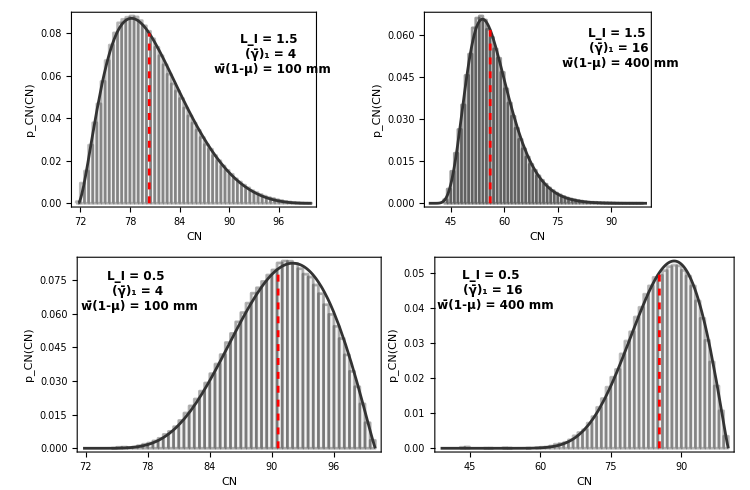
-Graphics-Wet Climate ------------------> Dry ClimateShallow Storage Capacity -------------------> Deep Storage Capacity

```mathematica
output=Labeled[Framed[Show[GraphicsGrid[{{part1,part2},{part3,part4}},Spacings->{-40,0}],ImageSize->750]],{Style["Wet Climate ------------------> Dry Climate",FontSize->16,Bold],Style["Shallow Storage Capacity -------------------> Deep Storage Capacity",FontSize->16,Bold]},{Left,Top},RotateLabel->True]
```

```mathematica
(*SetDirectory["C:/Users/Mark S. Bartlett/Dropbox/Research/ReverseJumps/LateX"];*)
SetDirectory[NotebookDirectory[]<>"Research"];
Export["Figure4.eps",output];
```

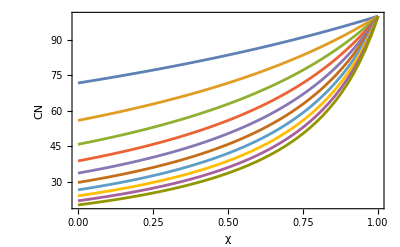

```mathematica
Plot[Evaluate[Table[25400./(10 w(1-x)+254),{w,10,100,10}]],{x,0,1},PlotRange->All, Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"CN",""},{"χ",""}}]
```